```mathematica
<< Задача 1.2.7 >>
Условие:
-Graphics-
Решение:
<<Распишем данные уравнения ускорений по координатам от времени >>
```

```mathematica
D[x[t], t,t] = -κ x[t] + Ω D[y[t], t]
D[y[t], t,t] = -κ y[t]  - Ω D[x[t], t]
```

-κ x[t]+Ω y'[t]

-κ y[t]-Ω x'[t]

```mathematica
<< Для нахождения уравнения движения, проинтегрируем уравнения, записанные выше, тем самым происходит переход к решению дифуров >>
```

```mathematica
FullSimplify[DSolve[{D[x[t], t,t] == -κ x[t] + Ω D[y[t], t],D[y[t], t,t] == -κ y[t]  - Ω D[x[t], t], x[0] == x0, y[0] ==0, x'[0] == 0,  y'[0]== v0},{x[t],y[t]},t]]
```

{{x[t]→((-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(2 √(4 κ Ω^2+Ω^4)),y[t]→(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))+((2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4))))/(√2 √(4 κ Ω^2+Ω^4))}}

```mathematica
DSolve[{True,True,x0==x[0],y[0]==0,x'[0]==0,v0==y'[0]},{((-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(2 √(4 κ Ω^2+Ω^4)),(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))+((2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4))))/(√2 √(4 κ Ω^2+Ω^4))},t]
```

```mathematica
<< Получаем уравнения движения Маятника Фуко >>
```

```mathematica
x[t]=((-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(2 √(4 κ Ω^2+Ω^4))
y[t]=(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))+((2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4))))/(√2 √(4 κ Ω^2+Ω^4))
```

((-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(2 √(4 κ Ω^2+Ω^4))

(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))+((2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4))))/(√2 √(4 κ Ω^2+Ω^4))

```mathematica
<< Корень из суммы квадратов скоростей по осям X и Y будет полной скоростью маятника Фуко. Найдем ее >>
```

```mathematica
V = FullSimplify[√((D[x[t], t])^2 +(D[y[t], t])^2)]
```

1/2 √(1/(4 κ Ω^2+Ω^4)(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2+1/2 (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2))

```mathematica
<< Для нахождения тангенциальное ускорения воспользуемся тем,что оно равно производной модуля вектора скорости 
(т. е. полной скорости) по времени, поскольку оно отвечает за приращение скорости за промежуток времени, то есть  изменение величины скорости >>
```

```mathematica
Atan= FullSimplify[D[V, t]]
```

(Ω^2 (v0^2-x0^2 κ+v0 x0 Ω) (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (4 κ+Ω^2-√(4 κ Ω^2+Ω^4)) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)] Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (4 κ+Ω^2+√(4 κ Ω^2+Ω^4)) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)] Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)]))/(√2 (4 κ Ω^2+Ω^4) √(1/(4 κ Ω^2+Ω^4)(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2+1/2 (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2)))

```mathematica
<< По аналогии с тем, что уже делали: полное ускорение маятника Фуко - это корень из суммы квадратов ускорений по осям X и Y >>
```

```mathematica
Afull = FullSimplify[√((D[x[t], t,t])^2 + (D[y[t], t,t])^2)]
```

1/2 √(1/(4 κ Ω^2+Ω^4)(1/4 ((2 κ+Ω^2+√(4 κ Ω^2+Ω^4)) (-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]-(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2+1/2 (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2))

```mathematica
<<Для построения ускорения можно воспользоваться теоремой Пифагора из курса школьной геометрии. Тогда тангенциальное и нормальное  ускорение - это катеты, а полное ускорение- гипотенуза : Anorm^2 + Atan^2  =A^2 , таким образом находим нормальное ускорение >>
```

```mathematica
Anorm = √((Afull)^2 - (Atan)^2)
```

√(1/(4 (4 κ Ω^2+Ω^4))(1/4 ((2 κ+Ω^2+√(4 κ Ω^2+Ω^4)) (-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]-(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2+1/2 (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2)-(Ω^4 (v0^2-x0^2 κ+v0 x0 Ω)^2 (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (4 κ+Ω^2-√(4 κ Ω^2+Ω^4)) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)] Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (4 κ+Ω^2+√(4 κ Ω^2+Ω^4)) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)] Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2)/(2 (4 κ Ω^2+Ω^4) (((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2+1/2 (√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)) (-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)) (2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])^2)))

```mathematica
<<Наконец-то построим траекторию нашего маятника>>
```

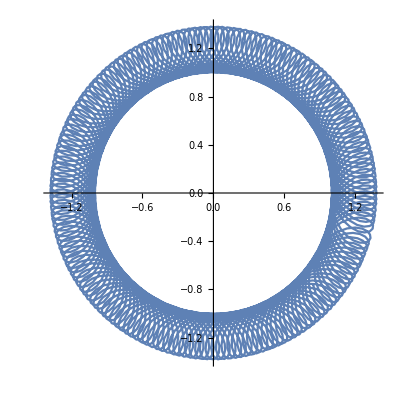

```mathematica
ParametricPlot[{((-2 v0 Ω+x0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)]+(2 v0 Ω+x0 (Ω^2+√(4 κ Ω^2+Ω^4))) Cosh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(2 √(4 κ Ω^2+Ω^4)),(((-2 x0 κ Ω+v0 (Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2-√(4 κ Ω^2+Ω^4)))+((2 x0 κ Ω+v0 (-Ω^2+√(4 κ Ω^2+Ω^4))) Sinh[(t √(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4)))/(√2)])/(√(-2 κ-Ω^2+√(4 κ Ω^2+Ω^4))))/(√2 √(4 κ Ω^2+Ω^4))}/.{x0->1,κ->1,Ω->π,v0->1},{t,0,300}]
```